### Programa para leer datos .txt obtenidos en CST

```mathematica
lambdaRange=Range[400,700,50];
```

```mathematica
(*Funcion para importar los datos*)
importDataC[dir_]:=Module[{data,freq,lambda,lambda0,dataCabs0,dataCsca0,dataCabs,dataCsca},
data=Import[dir];
freq=Drop[Drop[data[[All,1]],{1,5}],{8,19}];
lambda=0.2418*h c/freq;
lambda0=Range[700,400,-50];
dataCabs0=Drop[Drop[data[[All,2]],{1,5}],{8,19}];
dataCsca0=Drop[data[[All,2]],{1,17}];
dataCabs=Sort[Transpose[{lambda0,dataCabs0}]];
dataCsca=Sort[Transpose[{lambda0,dataCsca0}]];{dataCabs,dataCsca}]
```

```mathematica
importDataQ[dir_]:=Module[{data,freq,lambda,lambda0,dataCabs0,dataCsca0,dataCabs,dataCsca},
data=Import[dir];
freq=Drop[Drop[data[[All,1]],{1,5}],{8,19}];
lambda=0.2418*h c/freq;
lambda0=Range[700,400,-50];
dataCabs0=Drop[Drop[data[[All,2]],{1,5}],{8,19}]/(Pi*(2680)^2);
dataCsca0=Drop[data[[All,2]],{1,17}]/(Pi*(2680)^2);
dataCabs=Sort[Transpose[{lambda0,dataCabs0}]];
dataCsca=Sort[Transpose[{lambda0,dataCsca0}]];{dataCabs,dataCsca}]
```

```mathematica
(*Funcion error absoluto*)
```

```mathematica
errorAbs[data1_,data2_]:=Module[{error},
error=Abs[data1-data2]]
errorRel[data1_,data2_]:=Module[{error},
error=100*Abs[data1-data2]/data2]
```

## Background

```mathematica
bck1000=importDataQ["C:\\Users\\Nanoplasmonics\\Documents\\GitHub\\Tesis-de-Licenciatura\\CST\\Convergencia\\Background\\1000.csv"];
bck1500=importDataQ["C:\\Users\\Nanoplasmonics\\Documents\\GitHub\\Tesis-de-Licenciatura\\CST\\Convergencia\\Background\\1500.csv"];
bck2000=importDataQ["C:\\Users\\Nanoplasmonics\\Documents\\GitHub\\Tesis-de-Licenciatura\\CST\\Convergencia\\Background\\2000.csv"];
bck2500=importDataQ["C:\\Users\\Nanoplasmonics\\Documents\\GitHub\\Tesis-de-Licenciatura\\CST\\Convergencia\\Background\\2500.csv"];
```

```mathematica
eriCabsMie=Table[{λ,mieQabs[nindexEri30[λ],1.8235,2680,λ][[3]]},{λ,400,700,50}];
eriCscaMie=Table[{λ,mieQsca[nindexEri30[λ],1.8235,2680,λ][[3]]},{λ,400,700,50}];
eriQabsMie=Table[{λ,mieQabs[nindexEri30[λ],1.8235,2680,λ][[4]]},{λ,400,700,50}];
eriQscaMie=Table[{λ,mieQsca[nindexEri30[λ],1.8235,2680,λ][[4]]},{λ,400,700,50}];
```

```mathematica
error1Abs=errorAbs[bck1000[[1]][[All,2]],eriCabsMie[[All,2]]]
error2Abs=bck1500[[1]][[All,2]]-eriCabsMie[[All,2]];
error3Abs=bck2000[[1]][[All,2]]-eriCabsMie[[All,2]];
error1Sca=bck1000[[2]][[All,2]]-eriCscaMie[[All,2]];
error2Sca=bck1500[[2]][[All,2]]-eriCscaMie[[All,2]];
error3Sca=bck2000[[2]][[All,2]]-eriCscaMie[[All,2]];
```

{6.35071×10^6,2.61035×10^6,643812.,2.03332×10^6,736226.,239646.,83979.5}

```mathematica
Mean[errorAbs[bck1000[[1]][[All,2]],eriCabsMie[[All,2]]]]
Mean[errorAbs[bck1500[[1]][[All,2]],eriCabsMie[[All,2]]]]
Mean[errorAbs[bck2000[[1]][[All,2]],eriCabsMie[[All,2]]]]
Mean[errorAbs[bck2500[[1]][[All,2]],eriCabsMie[[All,2]]]]
```

2.32467×10^6

2.32467×10^6

2.32467×10^6

«1 more identical outputs»

```mathematica
Mean[errorAbs[bck1000[[2]][[All,2]],eriCscaMie[[All,2]]]]
Mean[errorAbs[bck1500[[2]][[All,2]],eriCscaMie[[All,2]]]]
Mean[errorAbs[bck2000[[2]][[All,2]],eriCscaMie[[All,2]]]]
Mean[errorAbs[bck2500[[2]][[All,2]],eriCscaMie[[All,2]]]]
```

1.8759×10^7

1.8759×10^7

1.88471×10^7

1.90222×10^7

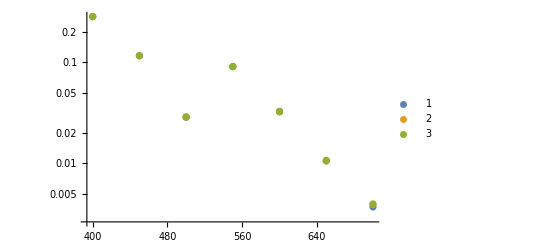

```mathematica
ListPlot[{Transpose[{lambdaRange,errorAbs[bck1000[[1]][[All,2]],eriQabsMie[[All,2]]]}],Transpose[{lambdaRange,errorAbs[bck2000[[1]][[All,2]],eriQabsMie[[All,2]]]}],Transpose[{lambdaRange,errorAbs[bck2500[[1]][[All,2]],eriQabsMie[[All,2]]]}]},ScalingFunctions->"Log",PlotLegends->Automatic]
```

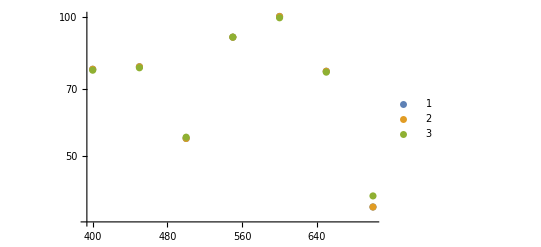

```mathematica
ListPlot[{Transpose[{lambdaRange,errorRel[bck1000[[1]][[All,2]],eriQabsMie[[All,2]]]}],Transpose[{lambdaRange,errorRel[bck1500[[1]][[All,2]],eriQabsMie[[All,2]]]}],Transpose[{lambdaRange,errorRel[bck2000[[1]][[All,2]],eriQabsMie[[All,2]]]}]},ScalingFunctions->"Log",PlotLegends->Automatic]
```

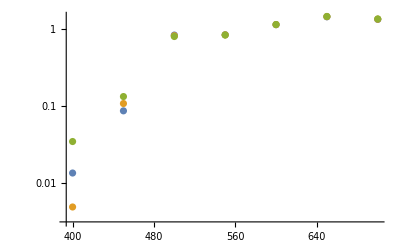

```mathematica
ListPlot[{Transpose[{lambdaRange,errorAbs[bck1500[[2]][[All,2]],eriQscaMie[[All,2]]]}],Transpose[{lambdaRange,errorAbs[bck2000[[2]][[All,2]],eriQscaMie[[All,2]]]}],Transpose[{lambdaRange,errorAbs[bck2500[[2]][[All,2]],eriQscaMie[[All,2]]]}]},ScalingFunctions->"Log",PlotRange->All]
```

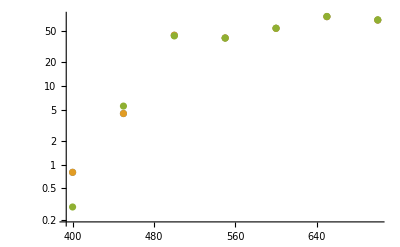

```mathematica
ListPlot[{Transpose[{lambdaRange,errorRel[bck1000[[2]][[All,2]],eriQscaMie[[All,2]]]}],Transpose[{lambdaRange,errorRel[bck1500[[2]][[All,2]],eriQscaMie[[All,2]]]}],Transpose[{lambdaRange,errorRel[bck2000[[2]][[All,2]],eriQscaMie[[All,2]]]}]},ScalingFunctions->"Log",PlotRange->All]
```

## PML

```mathematica
pml1000=importDataQ["C:\\Users\\Nanoplasmonics\\Documents\\GitHub\\Tesis-de-Licenciatura\\CST\\Convergencia\\PML\\1000.csv"];
pml1500=importDataQ["C:\\Users\\Nanoplasmonics\\Documents\\GitHub\\Tesis-de-Licenciatura\\CST\\Convergencia\\PML\\1500.csv"];
pml2000=importDataQ["C:\\Users\\Nanoplasmonics\\Documents\\GitHub\\Tesis-de-Licenciatura\\CST\\Convergencia\\PML\\2000.csv"];
pml2500=importDataQ["C:\\Users\\Nanoplasmonics\\Documents\\GitHub\\Tesis-de-Licenciatura\\CST\\Convergencia\\PML\\2500.csv"];
```

```mathematica
pmlBCK2000=importDataQ["C:\\Users\\Nanoplasmonics\\Documents\\GitHub\\Tesis-de-Licenciatura\\CST\\Convergencia\\PML_BCK_2000.csv"];
```

```mathematica
pmlBCK2000[[1]]
```

{{400,1.45813×10^7},{450,5.95217×10^6},{500,1.8209×10^6},{550,4.28091×10^6},{600,1.47043×10^6},{650,553468.},{700,299843.},{750,191972.},{800,138733.}}

```mathematica
Mean[errorAbs[pml1000[[1]][[All,2]],eriQabsMie[[All,2]]]]
Mean[errorAbs[pml1500[[1]][[All,2]],eriQabsMie[[All,2]]]]
Mean[errorAbs[pml2000[[1]][[All,2]],eriQabsMie[[All,2]]]]
Mean[errorAbs[pml2500[[1]][[All,2]],eriQabsMie[[All,2]]]]
```

0.0801659

0.0803932

0.0801458

0.0802124

```mathematica
Mean[errorAbs[pml1000[[2]][[All,2]],eriQscaMie[[All,2]]]]
Mean[errorAbs[pml1500[[2]][[All,2]],eriQscaMie[[All,2]]]]
Mean[errorAbs[pml2000[[2]][[All,2]],eriQscaMie[[All,2]]]]
Mean[errorAbs[pml2500[[2]][[All,2]],eriQscaMie[[All,2]]]]
```

0.805211

0.807146

0.809206

0.816287

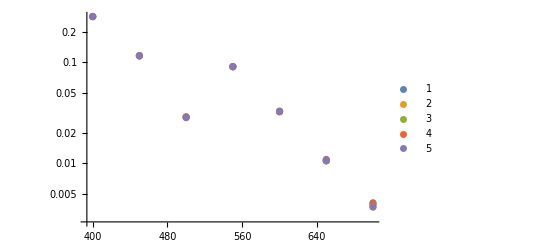

```mathematica
ListPlot[{Transpose[{lambdaRange,errorAbs[pml1000[[1]][[All,2]],eriQabsMie[[All,2]]]}],Transpose[{lambdaRange,errorAbs[pml1500[[1]][[All,2]],eriQabsMie[[All,2]]]}],Transpose[{lambdaRange,errorAbs[pml2000[[1]][[All,2]],eriQabsMie[[All,2]]]}],Transpose[{lambdaRange,errorAbs[pml2500[[1]][[All,2]],eriQabsMie[[All,2]]]}],
Transpose[{lambdaRange,errorAbs[pmlBCK2000[[1]][[All,2]],eriQabsMie[[All,2]]]}]},ScalingFunctions->"Log",PlotLegends->Automatic]
```

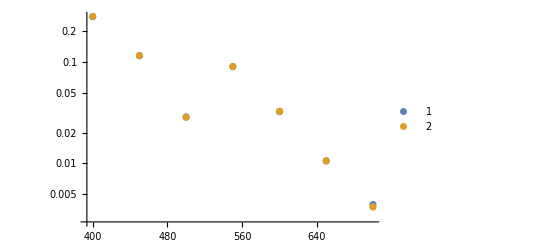

```mathematica
ListPlot[{Transpose[{lambdaRange,errorAbs[pml2000[[1]][[All,2]],eriQabsMie[[All,2]]]}],
Transpose[{lambdaRange,errorAbs[pmlBCK2000[[1]][[All,2]],eriQabsMie[[All,2]]]}]},ScalingFunctions->"Log",PlotLegends->Automatic]
```

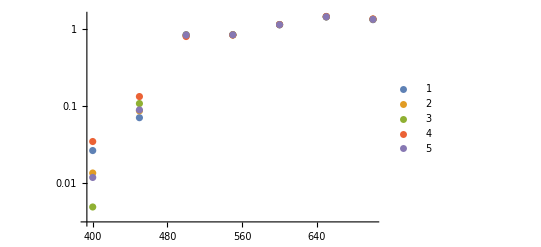

```mathematica
ListPlot[{Transpose[{lambdaRange,errorAbs[pml1000[[2]][[All,2]],eriQscaMie[[All,2]]]}],Transpose[{lambdaRange,errorAbs[pml1500[[2]][[All,2]],eriQscaMie[[All,2]]]}],Transpose[{lambdaRange,errorAbs[pml2000[[2]][[All,2]],eriQscaMie[[All,2]]]}],
Transpose[{lambdaRange,errorAbs[pml2500[[2]][[All,2]],eriQscaMie[[All,2]]]}],
Transpose[{lambdaRange,errorAbs[pmlBCK2000[[2]][[All,2]],eriQscaMie[[All,2]]]}]},ScalingFunctions->"Log",PlotRange->All,PlotLegends->Automatic]
```

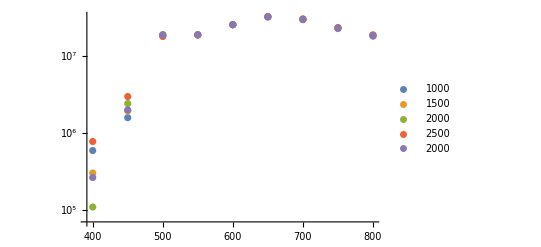

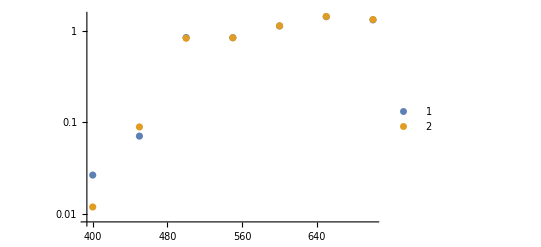

```mathematica
ListPlot[{Transpose[{lambdaRange,errorAbs[pml1000[[2]][[All,2]],eriQscaMie[[All,2]]]}],
Transpose[{lambdaRange,errorAbs[pmlBCK2000[[2]][[All,2]],eriQscaMie[[All,2]]]}]},ScalingFunctions->"Log",PlotRange->All,PlotLegends->Automatic]
```

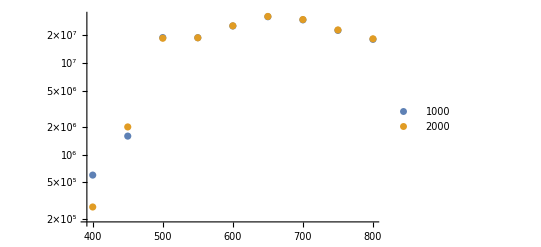

```mathematica
0.2418*h c/0.611821343
```

490.341

## Mesh

```mathematica
0.2418*h c/0.66620546222222
```

450.314

```mathematica
mesh150015002520=Import["C:\\Users\\Nanoplasmonics\\Documents\\GitHub\\Tesis-de-Licenciatura\\CST\\Convergencia\\Mesh\\1500_1500_25_20.csv"];
lambda0mesh150015002520=Range[700,400,-50];
lambda1mesh150015002520=Range[700,500,-50];
dataCabs0mesh150015002520=Drop[Drop[mesh150015002520[[All,2]],{1,3}],{8,17}]/(Pi*(2680)^2);
dataCabsmesh150015002520=Sort[Transpose[{lambda0mesh150015002520,dataCabs0mesh150015002520}]]
dataCsca0mesh150015002520=Drop[mesh150015002520[[All,2]],{1,15}]/(Pi*(2680)^2);
dataCscamesh1500150025200=Sort[Transpose[{lambda1mesh150015002520,dataCsca0mesh150015002520}]]
```

{{400,0.670151},{450,0.284396},{500,0.108743},{550,0.188632},{600,0.0614393},{650,0.024481},{700,0.0189341}}

{{500,1.53597},{550,1.65261},{600,1.95709},{650,2.25416},{700,2.51836}}

```mathematica
mesh150015002015=Import["C:\\Users\\Nanoplasmonics\\Documents\\GitHub\\Tesis-de-Licenciatura\\CST\\Convergencia\\Mesh\\1500_1500_20_15.csv"];
lambda0mesh150015002015=Range[700,400,-50];
lambda1mesh150015002015=Range[700,500,-50];
dataCabs0mesh150015002015=Drop[Drop[mesh150015002015[[All,2]],{1,3}],{8,17}]/(Pi*(2680)^2);
dataCabsmesh150015002015=Sort[Transpose[{lambda0mesh150015002015,dataCabs0mesh150015002015}]]
dataCsca0mesh150015002015=Drop[mesh150015002015[[All,2]],{1,15}]/(Pi*(2680)^2);
dataCscamesh1500150020150=Sort[Transpose[{lambda1mesh150015002015,dataCsca0mesh150015002015}]]
```

{{400,0.670151},{450,0.284396},{500,0.108743},{550,0.188632},{600,0.0614393},{650,0.024481},{700,0.0189341}}

{{500,1.53597},{550,1.65261},{600,1.95709},{650,2.25416},{700,2.51836}}

```mathematica
mesh15001500nolocal=Import["C:\\Users\\Nanoplasmonics\\Documents\\GitHub\\Tesis-de-Licenciatura\\CST\\Convergencia\\Mesh\\1500_1500_no_local.csv"];
lambda0mesh15001500nolocal=Range[700,400,-50];
lambda1mesh15001500nolocal=Range[700,500,-50];
dataCabs0mesh15001500nolocal=Drop[Drop[mesh15001500nolocal[[All,2]],{1,3}],{8,17}]/(Pi*(2680)^2);
dataCabsmesh15001500nolocal=Sort[Transpose[{lambda0mesh15001500nolocal,dataCabs0mesh15001500nolocal}]]
dataCsca0mesh15001500nolocal=Drop[mesh15001500nolocal[[All,2]],{1,15}]/(Pi*(2680)^2);
dataCscamesh15001500nolocal0=Sort[Transpose[{lambda1mesh15001500nolocal,dataCsca0mesh15001500nolocal}]]
```

{{400,0.669809},{450,0.284259},{500,0.108695},{550,0.188551},{600,0.0614007},{650,0.0244477},{700,0.0189088}}

{{500,1.53716},{550,1.65329},{600,1.956},{650,2.25344},{700,2.51845}}

```mathematica
dataCscamesh1500200020151=Transpose[{{400,450},{34652962.044491/(Pi*(2680)^2),37396871.024578/(Pi*(2680)^2)}}]
dataCscamesh1500200025201=Transpose[{{400,450},{34652962.044491/(Pi*(2680)^2),37396871.024578/(Pi*(2680)^2)}}]
dataCscamesh15002000nolocal1=Transpose[{{400,450},{34670770.635787/(Pi*(2680)^2),37406178.563308/(Pi*(2680)^2)}}]
```

{{400,1.53575},{450,1.65736}}

{{400,1.53575},{450,1.65736}}

{{400,1.53654},{450,1.65777}}

```mathematica
dataCscamesh150020002015=Join[dataCscamesh1500200020151,dataCscamesh1500150020150];
dataCscamesh150020002520=Join[dataCscamesh1500200025201,dataCscamesh1500150025200];
dataCscamesh15002000nolocal=Join[dataCscamesh15002000nolocal1,dataCscamesh15001500nolocal0];
```

# Datos bien

```mathematica
lambda=Range[400,600,4];
eriCabsMie=Table[{λ,mieQabs[nindexEriFit[λ],Sqrt[1.823],2680,λ][[3]]},{λ,400,600,1}];
eriCscaMie=Table[{λ,mieQsca[nindexEriFit[λ],Sqrt[1.823],2680,λ][[3]]},{λ,400,600,1}];
eriCextMie=Table[{λ,mieQext[nindexEriFit[λ],Sqrt[1.823],2680,λ][[3]]},{λ,400,600,1}];
eriQabsMie=Table[{λ,mieQabs[nindexEriFit[λ],Sqrt[1.823],2680,λ][[4]]},{λ,400,600,4}];
eriQscaMie=Table[{λ,mieQsca[nindexEriFit[λ],Sqrt[1.823],2680,λ][[4]]},{λ,400,600,4}];
eriQextMie=Table[{λ,mieQext[nindexEriFit[λ],Sqrt[1.823],2680,λ][[4]]},{λ,400,600,4}];
```

```mathematica
interpCabsMie=Interpolation[eriCabsMie];
```

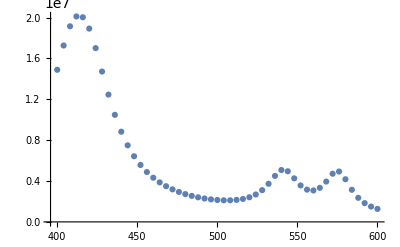

```mathematica
ListPlot[eriCabsMie]
```

```mathematica
FindMaximum[interpCabsMie[x],{x,400,430}]
FindMaximum[interpCabsMie[x],{x,530,550}]
FindMaximum[interpCabsMie[x],{x,560,580}]
```

{2.02024×10^7,{x→413.694}}

{5.10856×10^6,{x→541.213}}

{4.95125×10^6,{x→575.116}}

## PML

```mathematica
dataQext[dataCabs_,dataCsca_]:=Module[{dataCext},
dataCext=Transpose[{dataCabs[[All,1]],dataCabs[[All,2]]+dataCsca[[All,2]]}]]
```

```mathematica
dataPMLCabs=Import["C:\\Users\\Nanoplasmonics\\Documents\\GitHub\\Tesis-de-Licenciatura\\CST\\Convergencia_bien\\Matriz_Cabs.csv"];
dataPMLCsca=Import["C:\\Users\\Nanoplasmonics\\Documents\\GitHub\\Tesis-de-Licenciatura\\CST\\Convergencia_bien\\Matriz_Csca.csv"];

dataCabsPML500=Transpose[{dataPMLCabs[[All,1]],dataPMLCabs[[All,2]]/(Pi*2680^2)}];
dataCabsPML1000=Transpose[{dataPMLCabs[[All,1]],dataPMLCabs[[All,3]]/(Pi*2680^2)}];
dataCabsPML1230=Transpose[{dataPMLCabs[[All,1]],dataPMLCabs[[All,4]]/(Pi*2680^2)}];
dataCabsPML1470=Transpose[{dataPMLCabs[[All,1]],dataPMLCabs[[All,5]]/(Pi*2680^2)}];
dataCabsPML1720=Transpose[{dataPMLCabs[[All,1]],dataPMLCabs[[All,6]]/(Pi*2680^2)}];
dataCabsPML2300=Transpose[{dataPMLCabs[[All,1]],dataPMLCabs[[All,7]]/(Pi*2680^2)}];
```

```mathematica
dataCscaPML500=Transpose[{dataPMLCabs[[All,1]],dataPMLCsca[[All,2]]/(Pi*2680^2)}];
dataCscaPML1000=Transpose[{dataPMLCabs[[All,1]],dataPMLCsca[[All,3]]/(Pi*2680^2)}];
dataCscaPML1230=Transpose[{dataPMLCabs[[All,1]],dataPMLCsca[[All,4]]/(Pi*2680^2)}];
dataCscaPML1470=Transpose[{dataPMLCabs[[All,1]],dataPMLCsca[[All,5]]/(Pi*2680^2)}];
dataCscaPML1720=Transpose[{dataPMLCabs[[All,1]],dataPMLCsca[[All,6]]/(Pi*2680^2)}];
dataCscaPML2300=Transpose[{dataPMLCabs[[All,1]],dataPMLCsca[[All,7]]/(Pi*2680^2)}];
```

```mathematica
eriQabsMie2=Table[{λ,mieQabs[nindexEriFit[λ],Sqrt[1.8235],2680,λ][[4]]},{λ,dataPMLCabs[[All,1]]}];
eriQscaMie2=Table[{λ,mieQsca[nindexEriFit[λ],Sqrt[1.8235],2680,λ][[4]]},{λ,dataPMLCabs[[All,1]]}];
eriQextMie2=Table[{λ,mieQext[nindexEriFit[λ],Sqrt[1.8235],2680,λ][[4]]},{λ,dataPMLCabs[[All,1]]}];
```

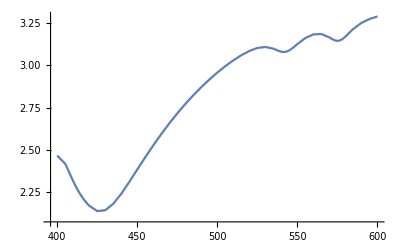

```mathematica
ListLinePlot[eriQextMie2]
```

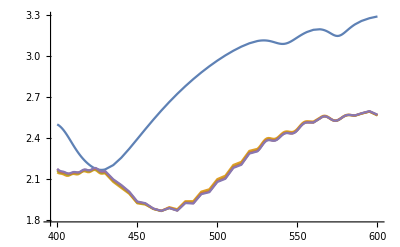

```mathematica
ListLinePlot[{eriQextMie2,dataQext[dataCabsPML500,dataCscaPML500],dataQext[dataCabsPML1000,dataCscaPML1000],dataQext[dataCabsPML1230,dataCscaPML1230],dataQext[dataCabsPML1470,dataCscaPML1470]}]
```

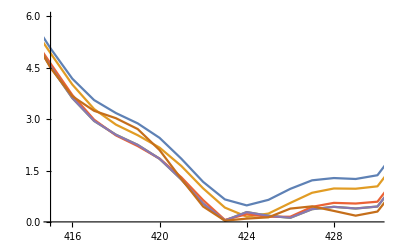

```mathematica
ListLinePlot[{Transpose[{dataPML[[All,1]],errorRel[dataQext[dataCabsPML500,dataCscaPML500][[All,2]],eriQextMie2[[All,2]]]}],Transpose[{dataPML[[All,1]],errorRel[dataQext[dataCabsPML1000,dataCscaPML1000][[All,2]],eriQextMie2[[All,2]]]}],Transpose[{dataPML[[All,1]],errorRel[dataQext[dataCabsPML1340,dataCscaPML1340][[All,2]],eriQextMie2[[All,2]]]}],
Transpose[{dataPML[[All,1]],errorRel[dataQext[dataCabsPML1470,dataCscaPML1470][[All,2]],eriQextMie2[[All,2]]]}],
Transpose[{dataPML[[All,1]],errorRel[dataQext[dataCabsPML1720,dataCscaPML1720][[All,2]],eriQextMie2[[All,2]]]}],
Transpose[{dataPML[[All,1]],errorRel[dataQext[dataCabsPML2300,dataCscaPML2300][[All,2]],eriQextMie2[[All,2]]]}]},PlotRange->{{415,430},{0,6}}]
```

```mathematica
Length[dataPML[[All,1]]]
```

77

```mathematica
Mean[Drop[Drop[errorRel[dataQext[dataCabsPML500,dataCscaPML500][[All,2]],eriQextMie2[[All,2]]],7],-60]]
Mean[Drop[Drop[errorRel[dataQext[dataCabsPML1000,dataCscaPML1000][[All,2]],eriQextMie2[[All,2]]],7],-60]]
Mean[Drop[Drop[errorRel[dataQext[dataCabsPML2300,dataCscaPML2300][[All,2]],eriQextMie2[[All,2]]],7],-60]]
```

12.7568

12.654

12.66

```mathematica
Mean[Drop[Drop[errorRel[dataQext[dataCabsPML500,dataCscaPML500][[All,2]],eriQextMie2[[All,2]]],49],-3]]
Mean[Drop[Drop[errorRel[dataQext[dataCabsPML1000,dataCscaPML1000][[All,2]],eriQextMie2[[All,2]]],49],-3]]
Mean[Drop[Drop[errorRel[dataQext[dataCabsPML2300,dataCscaPML2300][[All,2]],eriQextMie2[[All,2]]],49],-3]]
```

21.0424

21.2618

21.6334

```mathematica
Mean[Drop[Drop[errorRel[dataQext[dataCabsPML500,dataCscaPML500][[All,2]],eriQextMie2[[All,2]]],43],-27]]
Mean[Drop[Drop[errorRel[dataQext[dataCabsPML1000,dataCscaPML1000][[All,2]],eriQextMie2[[All,2]]],43],-27]]
Mean[Drop[Drop[errorRel[dataQext[dataCabsPML2000,dataCscaPML2000][[All,2]],eriQextMie2[[All,2]]],43],-27]]
```

21.2202

21.5238

21.6621

```mathematica
Drop[Drop[errorRel[dataQext[dataCabsPML500,dataCscaPML500][[All,2]],eriQextMie2[[All,2]]],43],-27]
```

{21.9754,21.5387,21.1699,20.9328,20.8588,20.9388,21.1272}

```mathematica
Mean[errorRel[dataQext[dataCabsPML500,dataCscaPML500][[All,2]],eriQextMie2[[All,2]]]]
Mean[errorRel[dataQext[dataCabsPML1000,dataCscaPML1000][[All,2]],eriQextMie2[[All,2]]]]
Mean[errorRel[dataQext[dataCabsPML1340,dataCscaPML1340][[All,2]],eriQextMie2[[All,2]]]]
Mean[errorRel[dataQext[dataCabsPML1470,dataCscaPML1470][[All,2]],eriQextMie2[[All,2]]]]
Mean[errorRel[dataQext[dataCabsPML2000,dataCscaPML2000][[All,2]],eriQextMie2[[All,2]]]]
Mean[errorRel[dataQext[dataCabsPML3000,dataCscaPML3000][[All,2]],eriQextMie2[[All,2]]]]
```

17.8995

17.9874

17.9617

17.959

17.9755

18.0952

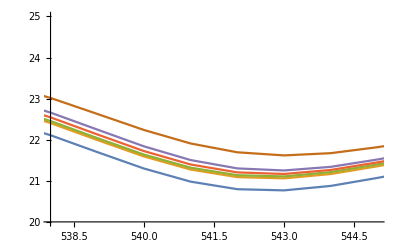

```mathematica
ListLinePlot[{Transpose[{dataPML[[All,1]],errorRel[dataQext[dataCabsPML500,dataCscaPML500][[All,2]],eriQextMie2[[All,2]]]}],Transpose[{dataPML[[All,1]],errorRel[dataQext[dataCabsPML1000,dataCscaPML1000][[All,2]],eriQextMie2[[All,2]]]}],Transpose[{dataPML[[All,1]],errorRel[dataQext[dataCabsPML1230,dataCscaPML1230][[All,2]],eriQextMie2[[All,2]]]}],
Transpose[{dataPML[[All,1]],errorRel[dataQext[dataCabsPML1470,dataCscaPML1470][[All,2]],eriQextMie2[[All,2]]]}],
Transpose[{dataPML[[All,1]],errorRel[dataQext[dataCabsPML1720,dataCscaPML1720][[All,2]],eriQextMie2[[All,2]]]}],
Transpose[{dataPML[[All,1]],errorRel[dataQext[dataCabsPML2300,dataCscaPML2300][[All,2]],eriQextMie2[[All,2]]]}]},PlotRange->{{538,545},{20,25}}]
```

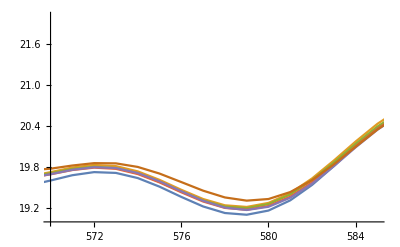

```mathematica
ListLinePlot[{Transpose[{dataPML[[All,1]],errorRel[dataQext[dataCabsPML500,dataCscaPML500][[All,2]],eriQextMie2[[All,2]]]}],Transpose[{dataPML[[All,1]],errorRel[dataQext[dataCabsPML1000,dataCscaPML1000][[All,2]],eriQextMie2[[All,2]]]}],Transpose[{dataPML[[All,1]],errorRel[dataQext[dataCabsPML1230,dataCscaPML1230][[All,2]],eriQextMie2[[All,2]]]}],
Transpose[{dataPML[[All,1]],errorRel[dataQext[dataCabsPML1470,dataCscaPML1470][[All,2]],eriQextMie2[[All,2]]]}],
Transpose[{dataPML[[All,1]],errorRel[dataQext[dataCabsPML1720,dataCscaPML1720][[All,2]],eriQextMie2[[All,2]]]}],
Transpose[{dataPML[[All,1]],errorRel[dataQext[dataCabsPML2300,dataCscaPML2300][[All,2]],eriQextMie2[[All,2]]]}]},PlotRange->{{570,585},{19,22}}]
```

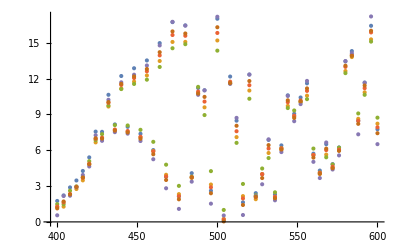

```mathematica
ListPlot[{Transpose[{lambda,errorRel[dataCabsPML500[[All,2]],eriCabsMie[[All,2]]]}],Transpose[{lambda,errorRel[dataCabsPML1000[[All,2]],eriCabsMie[[All,2]]]}],Transpose[{lambda,errorRel[dataCabsPML1500[[All,2]],eriCabsMie[[All,2]]]}],Transpose[{lambda,errorRel[dataCabsPML2000[[All,2]],eriCabsMie[[All,2]]]}],
Transpose[{lambda,errorRel[dataCabsPML2500[[All,2]],eriCabsMie[[All,2]]]}],
Transpose[{lambda,errorRel[dataCabsPML3000[[All,2]],eriCabsMie[[All,2]]]}]},PlotRange->All]
```

## Mesh

```mathematica
dataMeshCabs=Import["C:\\Users\\Nanoplasmonics\\Documents\\GitHub\\Tesis-de-Licenciatura\\CST\\Pruebas\\\Mesh variations\\Cabs.csv"];
dataMeshCsca=Import["C:\\Users\\Nanoplasmonics\\Documents\\GitHub\\Tesis-de-Licenciatura\\CST\\Pruebas\\Mesh variations\\Csca.csv"];

dataCabsMesh7=Transpose[{dataMeshCabs[[All,1]],dataMeshCabs[[All,2]]/(Pi*(2680^2))}];
dataCabsMesh10=Transpose[{dataMeshCabs[[All,1]],dataMeshCabs[[All,3]]/(Pi*(2680^2))}];
dataCabsMesh12=Transpose[{dataMeshCabs[[All,1]],dataMeshCabs[[All,4]]/(Pi*(2680^2))}];
dataCabsMesh15=Transpose[{dataMeshCabs[[All,1]],dataMeshCabs[[All,5]]/(Pi*(2680^2))}];
dataCabsMesh17=Transpose[{dataMeshCabs[[All,1]],dataMeshCabs[[All,6]]/(Pi*(2680^2))}];

dataCscaMesh7=Transpose[{dataMeshCsca[[All,1]],dataMeshCsca[[All,2]]/(Pi*(2680^2))}];
dataCscaMesh10=Transpose[{dataMeshCsca[[All,1]],dataMeshCsca[[All,3]]/(Pi*(2680^2))}];
dataCscaMesh12=Transpose[{dataMeshCsca[[All,1]],dataMeshCsca[[All,4]]/(Pi*(2680^2))}];
dataCscaMesh15=Transpose[{dataMeshCsca[[All,1]],dataMeshCsca[[All,5]]/(Pi*(2680^2))}];
dataCscaMesh17=Transpose[{dataMeshCsca[[All,1]],dataMeshCsca[[All,6]]/(Pi*(2680^2))}];
```

```mathematica
eriQabsMieMesh=Table[{λ,mieQabs[nindexEriFit[λ],Sqrt[1.8235],2680,λ][[4]]},{λ,dataMeshCabs[[All,1]]}];
eriQscaMieMesh=Table[{λ,mieQsca[nindexEriFit[λ],Sqrt[1.8235],2680,λ][[4]]},{λ,dataMeshCsca[[All,1]]}];
eriQextMieMesh=Table[{λ,mieQext[nindexEriFit[λ],Sqrt[1.8235],2680,λ][[4]]},{λ,dataMeshCsca[[All,1]]}];
```

```mathematica
eriQextMieMesh
```

{{400,2.4665},{405,2.41804},{406,2.39879},{407,2.37782},{408,2.35705},{409,2.33593},{410,2.31561},{411,2.29618},{412,2.27768},{413,2.26074},{414,2.24478},{415,2.22987},{416,2.21613},{417,2.20338},{418,2.19158},{419,2.18072},{420,2.17081},{425,2.1393},{430,2.14409},{435,2.18215},{440,2.24152},{445,2.31136},{450,2.38452},{455,2.4571},{460,2.52721},{465,2.59382},{470,2.65672},{475,2.71576},{480,2.771},{485,2.82263},{490,2.87068},{495,2.9153},{500,2.95659},{505,2.99441},{510,3.02867},{515,3.05884},{520,3.08391},{525,3.10156},{530,3.10766},{535,3.09738},{536,3.09358},{537,3.08956},{538,3.08565},{539,3.08218},{540,3.07955},{541,3.07812},{542,3.07817},{543,3.07984},{544,3.08315},{545,3.08795},{546,3.09401},{547,3.10102},{548,3.10867},{549,3.11666},{550,3.12472},{555,3.16045},{560,3.18168},{565,3.18375},{570,3.16369},{571,3.15804},{572,3.15266},{573,3.1481},{574,3.14494},{575,3.14369},{576,3.14466},{577,3.14793},{578,3.15331},{579,3.16042},{580,3.16879},{581,3.17792},{582,3.18736},{583,3.19676},{584,3.20589},{585,3.21457},{590,3.24961},{595,3.27253},{600,3.28751}}

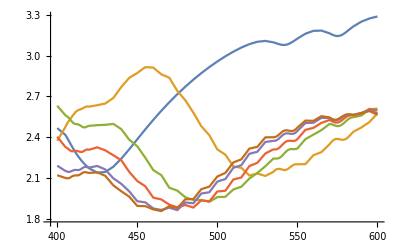

```mathematica
ListLinePlot[{eriQextMieMesh,dataQext[dataCabsMesh7,dataCscaMesh7],dataQext[dataCabsMesh10,dataCscaMesh10],dataQext[dataCabsMesh12,dataCscaMesh12],dataQext[dataCabsMesh15,dataCscaMesh15],dataQext[dataCabsMesh17,dataCscaMesh17]},PlotRange->All]
```

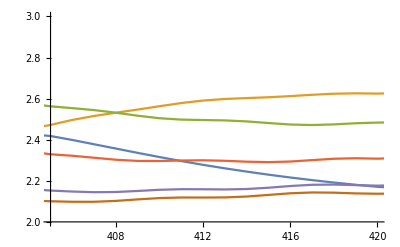

```mathematica
ListLinePlot[{eriQextMie2,dataQext[dataCabsMesh7,dataCscaMesh7],dataQext[dataCabsMesh10,dataCscaMesh10],dataQext[dataCabsMesh12,dataCscaMesh12],dataQext[dataCabsMesh15,dataCscaMesh15],dataQext[dataCabsMesh17,dataCscaMesh17]},PlotRange->{{405,420},{2,3}}]
```

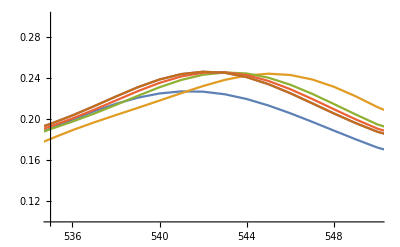

```mathematica
ListLinePlot[{eriQabsMieMesh,dataCabsMesh7,dataCabsMesh10,dataCabsMesh12,dataCabsMesh15,dataCabsMesh17},PlotRange->{{535,550},{0.1,0.3}}]
```

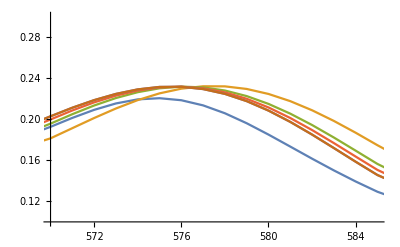

```mathematica
ListLinePlot[{eriQabsMieMesh,dataCabsMesh7,dataCabsMesh10,dataCabsMesh12,dataCabsMesh15,dataCabsMesh17},PlotRange->{{570,585},{0.1,0.3}}]
```

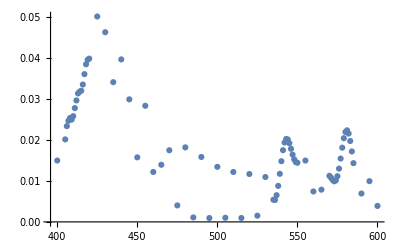

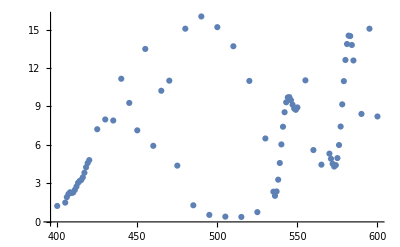

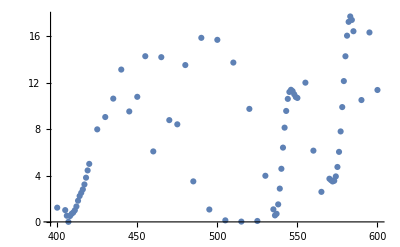

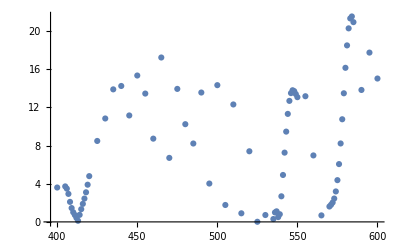

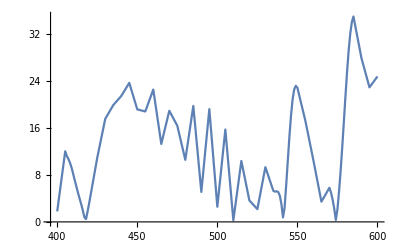

```mathematica
ListPlot[{Transpose[{dataCabsMesh17[[All,1]],errorAbs[dataCabsMesh17[[All,2]],eriQabsMieMesh[[All,2]]]}]},PlotRange->All]
ListPlot[{Transpose[{dataCabsMesh15[[All,1]],errorRel[dataCabsMesh15[[All,2]],eriQabsMieMesh[[All,2]]]}]},PlotRange->All]
ListPlot[{Transpose[{dataCabsMesh12[[All,1]],errorRel[dataCabsMesh12[[All,2]],eriQabsMieMesh[[All,2]]]}]},PlotRange->All]
ListPlot[{Transpose[{dataCabsMesh10[[All,1]],errorRel[dataCabsMesh10[[All,2]],eriQabsMieMesh[[All,2]]]}]},PlotRange->All]
ListLinePlot[{Transpose[{dataCabsMesh7[[All,1]],errorRel[dataCabsMesh7[[All,2]],eriQabsMieMesh[[All,2]]]}]},PlotRange->All]
```

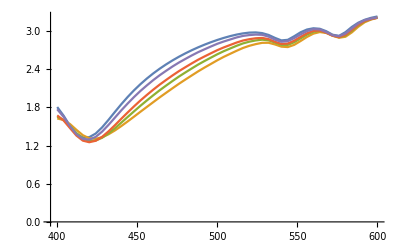

```mathematica
ListLinePlot[{eriQscaMie,dataCscaLocalMesh2520,dataCscaLocalMesh2015,dataCscaLocalMesh1510,dataCscaLocalMesh107},PlotRange->All]
```

```mathematica
(1.386471835872126-1.3779143880269906)/1.3779143880269906
```

0.00621044

```mathematica
eriQscaMie
dataCscaLocalMesh107
```

```mathematica
(2.8545177525645538-2.8332054766949604)/2.8332054766949604
```

0.00752232

## Local Mesh

```mathematica
dataLocalCabs=Import["C:\\Users\\Nanoplasmonics\\Documents\\GitHub\\Tesis-de-Licenciatura\\CST\\Convergencia_0\\Local_mesh\\Cabs.csv"];
dataLocalCsca=Import["C:\\Users\\Nanoplasmonics\\Documents\\GitHub\\Tesis-de-Licenciatura\\CST\\Convergencia_0\\Local_mesh\\Csca.csv"];
dataLocalCabsExp=Import["C:\\Users\\Nanoplasmonics\\Documents\\GitHub\\Tesis-de-Licenciatura\\CST\\Pruebas\\Cabs_exp.csv"];
dataLocalCscaExp=Import["C:\\Users\\Nanoplasmonics\\Documents\\GitHub\\Tesis-de-Licenciatura\\CST\\Pruebas\\Csca_exp.csv"];

dataCabsLocalMesh2520=Transpose[{dataLocalCabs[[All,1]],dataLocalCabs[[All,2]]/(Pi*(2680^2))}];
dataCabsLocalMesh1613=Transpose[{dataLocalCabs[[All,1]],dataLocalCabs[[All,3]]/(Pi*(2680^2))}];
dataCabsLocalMesh1510=Transpose[{dataLocalCabs[[All,1]],dataLocalCabs[[All,4]]/(Pi*(2680^2))}];
dataCabsLocalMesh107=Transpose[{dataLocalCabs[[All,1]],dataLocalCabs[[All,5]]/(Pi*(2680^2))}];
dataCabsLocalMesh73=Transpose[{dataLocalCabs[[All,1]],dataLocalCabs[[All,6]]/(Pi*(2680^2))}];
dataCabsLocalMesh2520Exp=Transpose[{dataLocalCabsExp[[All,1]],dataLocalCabsExp[[All,2]]/(Pi*(2680^2))}];

dataCscaLocalMesh2520=Transpose[{dataLocalCsca[[All,1]],dataLocalCsca[[All,2]]/(Pi*(2680^2))}];
dataCscaLocalMesh1613=Transpose[{dataLocalCabs[[All,1]],dataLocalCsca[[All,3]]/(Pi*(2680^2))}];
dataCscaLocalMesh1510=Transpose[{dataLocalCsca[[All,1]],dataLocalCsca[[All,4]]/(Pi*(2680^2))}];
dataCscaLocalMesh107=Transpose[{dataLocalCsca[[All,1]],dataLocalCsca[[All,5]]/(Pi*(2680^2))}];
dataCscaLocalMesh73=Transpose[{dataLocalCsca[[All,1]],dataLocalCsca[[All,6]]/(Pi*(2680^2))}];
dataCscaLocalMesh2520Exp=Transpose[{dataLocalCscaExp[[All,1]],dataLocalCscaExp[[All,2]]/(Pi*(2680^2))}];
```

```mathematica
eriQextMieLocalMesh=Table[{λ,mieQext[nindexEriFit[λ],Sqrt[1.8235],2680,λ][[4]]},{λ,dataLocalCsca[[All,1]]}];
```

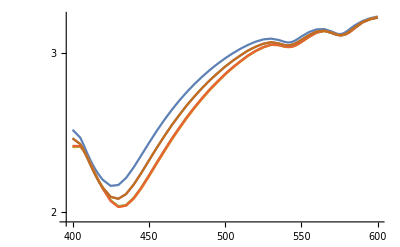

```mathematica
ListLinePlot[{eriQextMieLocalMesh,dataQext[dataCabsLocalMesh2520,dataCscaLocalMesh2520],dataQext[dataCabsLocalMesh1613,dataCscaLocalMesh1613],dataQext[dataCabsLocalMesh1510,dataCscaLocalMesh1510],dataQext[dataCabsLocalMesh107,dataCscaLocalMesh107],dataQext[dataCabsLocalMesh73,dataCscaLocalMesh73]},PlotRange->All,ScalingFunctions->"Log"]
```

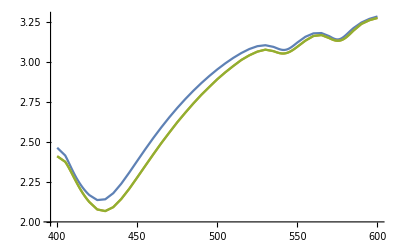

```mathematica
ListLinePlot[{eriQextMieLocalMesh,dataQext[dataCabsLocalMesh107,dataCscaLocalMesh107],dataQext[dataCabsLocalMesh73,dataCscaLocalMesh73]},PlotRange->All]
```

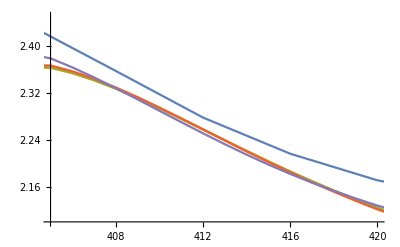

```mathematica
ListLinePlot[{eriQextMie,dataQext[dataCabsLocalMesh2520,dataCscaLocalMesh2520],dataQext[dataCabsLocalMesh1613,dataCscaLocalMesh1613],dataQext[dataCabsLocalMesh1510,dataCscaLocalMesh1510],dataQext[dataCabsLocalMesh107,dataCscaLocalMesh107]},PlotRange->{{405,420},{2.1,2.45}}]
```

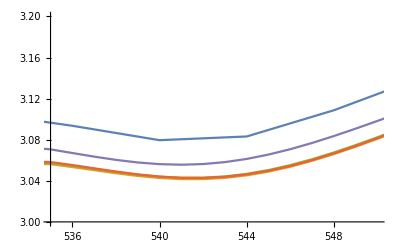

```mathematica
ListLinePlot[{eriQextMie,dataQext[dataCabsLocalMesh2520,dataCscaLocalMesh2520],dataQext[dataCabsLocalMesh1613,dataCscaLocalMesh1613],dataQext[dataCabsLocalMesh1510,dataCscaLocalMesh1510],dataQext[dataCabsLocalMesh107,dataCscaLocalMesh107]},PlotRange->{{535,550},{3,3.2}}]
```

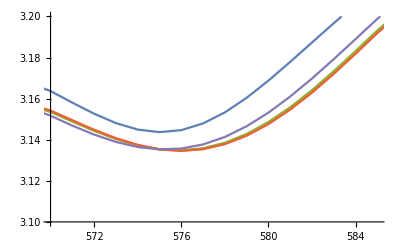

```mathematica
ListLinePlot[{eriQextMieLocalMesh,dataQext[dataCabsLocalMesh2520,dataCscaLocalMesh2520],dataQext[dataCabsLocalMesh1613,dataCscaLocalMesh1613],dataQext[dataCabsLocalMesh1510,dataCscaLocalMesh1510],dataQext[dataCabsLocalMesh107,dataCscaLocalMesh107]},PlotRange->{{570,585},{3.1,3.2}}]
```

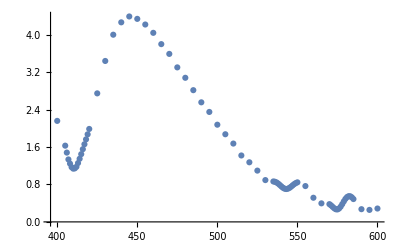

```mathematica
ListPlot[{Transpose[{dataCabsLocalMesh107[[All,1]],errorRel[dataQext[dataCabsLocalMesh107,dataCscaLocalMesh107][[All,2]],eriQextMieLocalMesh[[All,2]]]}]},PlotRange->All]
```

```mathematica
ListLinePlot[{eriQscaMie,dataCscaLocalMesh2520,dataCscaLocalMesh2015,dataCscaLocalMesh1510,dataCscaLocalMesh107},PlotRange->All]
```

-Graphics-

```mathematica
(1.386471835872126-1.3779143880269906)/1.3779143880269906
```

0.00621044

```mathematica
eriQscaMie
dataCscaLocalMesh107
```

```mathematica
(2.8545177525645538-2.8332054766949604)/2.8332054766949604
```

0.00752232

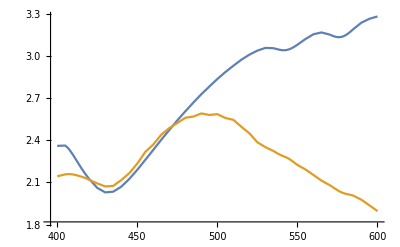

```mathematica
ListLinePlot[{dataQext[dataCabsLocalMesh2520,dataCscaLocalMesh2520],dataQext[dataCabsLocalMesh2520Exp,dataCscaLocalMesh2520Exp]}]
```

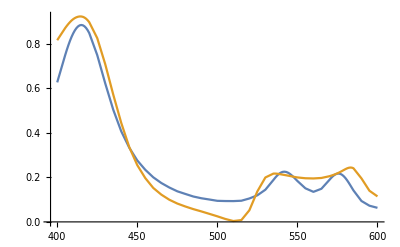

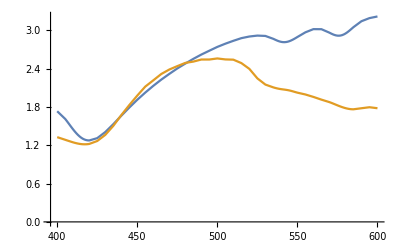

```mathematica
ListLinePlot[{dataCabsLocalMesh2520,dataCabsLocalMesh2520Exp}]
ListLinePlot[{dataCscaLocalMesh2520,dataCscaLocalMesh2520Exp}]
```

```mathematica
nindexEriExp[x_]:=parteRe30[h c/x]+I*parteIm30[h c/x]
```

```mathematica
nindexEriExp[400]
```

1.40718+0.00968558 ⅈ

3.10175

```mathematica
h
```

```mathematica
lambda30=Sort[Table[h c/x,{x,h c/600,h c/400,0.07}]]
```

{407.076,416.645,426.675,437.2,448.257,459.888,472.138,485.059,498.707,513.145,528.445,544.684,561.954,580.354,600.}

```mathematica
eriQextMieLocalMesh=Table[{λ,mieQext[nindexEriFit[λ],Sqrt[1.8235],2680,λ][[4]]},{λ,400,600,1}];
eriQextMieLocalMeshExp=Table[{λ,mieQext[nindexEriExp[λ],Sqrt[1.8235],2680,λ][[4]]},{λ,lambda30}];
```

InterpolatingFunction::dmval: Input value {2.06783} lies outside the range of data in the interpolating function. Extrapolation will be used.

```mathematica
eriQextMieLocalMeshExp
```

{{407.076,2.48602},{416.645,2.28964},{426.675,2.20663},{437.2,2.29559},{448.257,2.51363},{459.888,2.7552},{472.138,2.94097},{485.059,3.08267},{498.707,3.19205},{513.145,3.23112},{528.445,3.19365},{544.684,3.14409},{561.954,3.17567},{580.354,3.10653},{600.,3.22693}}

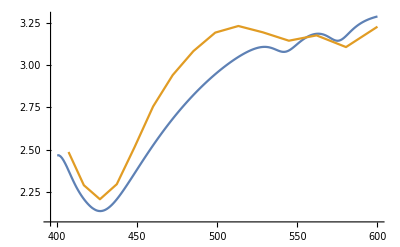

```mathematica
ListLinePlot[{eriQextMieLocalMesh,eriQextMieLocalMeshExp}]
```